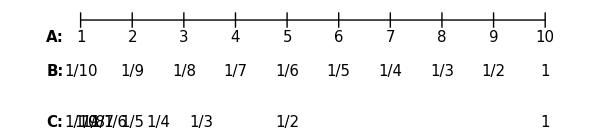

```mathematica
Graphics[{
Line[{{1,0},{10,0}}],
Table[{
Line[{{i,-0.15},{i,0.15}}],
Text[Style[i,15],{i,-0.35}],
Text[Style[1/(11-i),15],{i,-1.}],
Text[Style[1/(11-i),15],{(1/(11-i))*10,-2}]
},{i,1,10}],Text[Style["A:",15,Bold],{0.5,-0.35}],Text[Style["B:",15,Bold],{0.5,-1}],Text[Style["C:",15,Bold],{0.5,-2}]
},ImageSize->600]
```

line A: scale for space time (excluding 0)
line B: inverted and reversed A for space velocity, numbers in wrong location but how we want the spacing to look
line C: how B actually looks with numbers in the correct locations but spacing is not linear